# Independent spins

## Constants

```mathematica
const=1;
```

```mathematica
hbar=1;
Clear[phi,theta]
```

## Pauli Matrices

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,2}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0)}

## Spin 1/2

```mathematica
sx=1/2 PauliMatrix[1];
sy=1/2PauliMatrix[2];
(*sz=1/2PauliMatrix[3];*)
```

```mathematica
MatrixForm[sx]
```

(0 | 1/2
1/2 | 0)

```mathematica
{sx,sy(*,sz*)}=(1/2)*Table[PauliMatrix[i],{i,1,2}];
MatrixForm[#]&/@%
```

{(0 | 1/2
1/2 | 0),(0 | -ⅈ/2
ⅈ/2 | 0)}

## Spin - 1/2 Hamiltonian

```mathematica
-Graphics-;
```

### Hamiltonian

```mathematica
H[Bx_,By_(*,Bz_*)]=-const(sx*Bx+sy*By(*+sz*Bz*));
MatrixForm[%]
```

(0 | -Bx/2+(ⅈ By)/2
-Bx/2-(ⅈ By)/2 | 0)

```mathematica
(hamiltonian=H[Sin[theta]Cos[phi],Sin[theta]Sin[phi](*,Cos[theta]*)])//MatrixForm
```

(0 | -1/2 Cos[phi] Sin[theta]+1/2 ⅈ Sin[phi] Sin[theta]
-1/2 Cos[phi] Sin[theta]-1/2 ⅈ Sin[phi] Sin[theta] | 0)

## Diagonalization

```mathematica
Eigenvalues[hamiltonian]
```

{-Sin[theta]/2,Sin[theta]/2}

```mathematica
{ket1,ket2}=Eigenvectors[hamiltonian]//FullSimplify
```

{{ⅇ^(-ⅈ phi),1},{-ⅇ^(-ⅈ phi),1}}

### other way

```mathematica
{energies, kets}=Eigensystem[hamiltonian]//FullSimplify
```

{{-Sin[theta]/2,Sin[theta]/2},{{ⅇ^(-ⅈ phi),1},{-ⅇ^(-ⅈ phi),1}}}

## Check Orthogonality

```mathematica
ket1.ket2
```

1-ⅇ^(-2 ⅈ phi)

```mathematica
Conjugate[{ket1}].Transpose[{ket2}]//FullSimplify[#,Assumptions->Element[theta|phi,Reals]]&
```

{{0}}

### other way

```mathematica
kets[[1]]
```

{ⅇ^(-ⅈ phi),1}

```mathematica
kets[[2]]
```

{-ⅇ^(-ⅈ phi),1}

```mathematica
kets[[1]].kets[[2]]
```

1-ⅇ^(-2 ⅈ phi)

```mathematica
Conjugate[{kets[[1]]}].Transpose[{kets[[2]]}]//FullSimplify[#,Assumptions->Element[theta|phi,Reals]]&
```

{{0}}

## Propagator

```mathematica
-Graphics-;
```

### Initial state

```mathematica
psi0=1/(√2)({{1}, {1}});
```

### Time Evolution Operator

```mathematica
propU[t_]:=MatrixExp[-I/hbar  hamiltonian t];
```

## Example

### Field direction

```mathematica
theta=0;
phi=0;
```

### diagonalization

```mathematica
{energies, kets}=Eigensystem[hamiltonian]//FullSimplify
```

{{0,0},{{0,1},{1,0}}}

### time evolution operator

```mathematica
propU[t]//MatrixForm
```

(1 | 0
0 | 1)

### time dependent state

```mathematica
psi[t_]:=propU[t].psi0
```

```mathematica
psi[t]
```

{{1/(√2)},{1/(√2)}}

### projection onto initial state

```mathematica
proj=(ConjugateTranspose[psi0].psi[t])^2//FullSimplify
```

{{1}}

### Plot Rabi oscilations

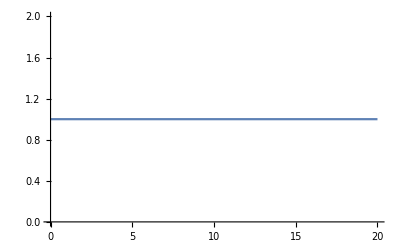

-Graphics-

```mathematica
Plot[proj,{t,0,20}]
```

# Interacting Spins: Heisenberg model for two spins

-Graphics-

-Graphics-

```mathematica
-Graphics-;
```

### KroneckerProduct

```mathematica
am=Array [Subscript[a, ##]&,{2,2}]
```

{{a_(1,1),a_(1,2)},{a_(2,1),a_(2,2)}}

```mathematica
bm=Array [Subscript[b, ##]&,{2,2}]
```

{{b_(1,1),b_(1,2)},{b_(2,1),b_(2,2)}}

```mathematica
KroneckerProduct[am,bm]//MatrixForm
```

(a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,2) b_(1,1) | a_(1,2) b_(1,2)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,2) b_(2,1) | a_(1,2) b_(2,2)
a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,2) b_(1,1) | a_(2,2) b_(1,2)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,2) b_(2,1) | a_(2,2) b_(2,2))

```mathematica
state1=Array [Subscript[c, ##]&,{2,1}]
```

{{c_(1,1)},{c_(2,1)}}

```mathematica
state2=Array [Subscript[d, ##]&,{2,1}]
```

{{d_(1,1)},{d_(2,1)}}

```mathematica
KroneckerProduct[state1,state2]//MatrixForm
```

(c_(1,1) d_(1,1)
c_(1,1) d_(2,1)
c_(2,1) d_(1,1)
c_(2,1) d_(2,1))

```mathematica
(Sx1=KroneckerProduct[sx,IdentityMatrix[2]])//MatrixForm;
(Sx2=KroneckerProduct[IdentityMatrix[2],sx])//MatrixForm;
(Sy1=KroneckerProduct[sy,IdentityMatrix[2]])//MatrixForm;
(Sy2=KroneckerProduct[IdentityMatrix[2],sy])//MatrixForm;
(Sz1=KroneckerProduct[sz,IdentityMatrix[2]])//MatrixForm;
(Sz2=KroneckerProduct[IdentityMatrix[2],sz])//MatrixForm
```

(1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/2)

```mathematica
heisenbergH=Jij(Sx1.Sx2+Sy1.Sy2+Sz1.Sz2);
%//MatrixForm
```

(Jij/4 | 0 | 0 | 0
0 | -Jij/4 | Jij/2 | 0
0 | Jij/2 | -Jij/4 | 0
0 | 0 | 0 | Jij/4)

```mathematica
values=Eigensystem[heisenbergH]// MatrixForm
```

(-(3 Jij)/4 | Jij/4 | Jij/4 | Jij/4
{0,-1,1,0} | {0,0,0,1} | {0,1,1,0} | {1,0,0,0})

```mathematica
estadoneel=KroneckerProduct[({{1}, {0}}),({{0}, {1}})];
%// MatrixForm
```

(0
1
0
0)

```mathematica
ConjugateTranspose[estadoneel].heisenbergH.estadoneel;
%// MatrixForm
```

(-Jij/4)

# Biliography

```mathematica
http://physics.bu.edu/~sandvik/nccu/l1.pdf
```

```mathematica
wikipedia
```

wikipedia

```mathematica
+
```